## Linear-time Kernel Stein Discrepancy

Evaluate the population kernel Stein discrepancy where p(x) = N(0, 1), and q(x)=N(mu_q, sigma_q^2).
Assume that a Gaussian kernel is used.

```mathematica
$Assumptions->{{Subscript[σ, k],Subscript[σ, q],κ}>0,Element[{Subscript[μ, q]},Reals]}
```

True→{{σ_k,σ_q,κ}>0,μ_q∈Reals}

```mathematica
Subscript[s, k]=κ^2
```

κ^2

## Variance under H_1

U-statistic kernel  h_p

```mathematica
Subscript[μ, p]=0
Subscript[σ, p]=1
```

0

1

```mathematica
logp[x_]:=-(x-Subscript[μ, p])^2/(2*Subscript[σ, p]^2)
ker[x_,y_,s_]:=Exp[-(x-y)^2/(2*s)]
Dkx[x_,y_,s_]:=D[ker[x,y,s],x]
Dky[x_,y_,s_]:=D[ker[x,y,s],y]
Dkxy[x_,y_,s_]:=D[Dkx[x,y,s],y]
```

```mathematica
h[x_,y_]:=logp'[x] ker[x,y,Subscript[s, k]] logp'[y]+logp'[y] Dkx[x,y,Subscript[s, k]]+ logp'[x] Dky[x,y,Subscript[s, k]]+Dkxy[x,y,Subscript[s, k]]
```

```mathematica
Simplify[h[x,y]]
```

(ⅇ^(-(x-y)^2/(2 κ^2)) (κ^2-x^2 (1+κ^2)-y^2 (1+κ^2)+x y (2+2 κ^2+κ^4)))/κ^4

```mathematica
exh = Expectation[h[x,y],x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

1/(√(1/κ^2+1/σ_q^2) σ_q (κ^2+σ_q^2)^2)ⅇ^(-(y-μ_q)^2/(2 (κ^2+σ_q^2))) (-(1+κ^2) μ_q^2+(-1+σ_q^2) (-κ^2+y^2 (1+κ^2)+(-1+y^2) σ_q^2)+y μ_q (2+2 κ^2+κ^4+κ^2 σ_q^2))

```mathematica
eh=Expectation[exh,y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(1+κ^2 μ_q^2+2 (-1+μ_q^2) σ_q^2+σ_q^4)/((κ^2+2 σ_q^2) √(1+(2 σ_q^2)/κ^2))

```mathematica
kstein=eh//Simplify
```

((-1+σ_q^2)^2+μ_q^2 (κ^2+2 σ_q^2))/((κ^2+2 σ_q^2) √(1+(2 σ_q^2)/κ^2))

```mathematica
Simplify[h[x,y]^2]
```

(ⅇ^(-(x-y)^2/κ^2) (κ^2-x^2 (1+κ^2)-y^2 (1+κ^2)+x y (2+2 κ^2+κ^4))^2)/κ^8

```mathematica
exph2 = Assuming[κ>0,Expectation[h[x,y]^2,x\[Distributed]NormalDistribution[Subscript[μ, p],Subscript[σ, p]]]]
```

1/(κ^3 (2+κ^2)^(9/2))ⅇ^(-y^2/(2+κ^2)) (12+4 (7+5 y^2) κ^2+(27+46 y^2+9 y^4) κ^4+2 (6+29 y^2+3 y^4) κ^6+(2+36 y^2+y^4) κ^8+10 y^2 κ^10+y^2 κ^12)

```mathematica
eph2=Assuming[κ>0,Expectation[exph2,y\[Distributed]NormalDistribution[Subscript[μ, p],Subscript[σ, p]]]]
```

(12+κ^2 (4+κ^2) (5+4 κ^2+κ^4))/(κ^3 (4+κ^2)^(5/2))

```mathematica
varph=eph2//Simplify
```

(12+κ^2 (4+κ^2) (5+4 κ^2+κ^4))/(κ^3 (4+κ^2)^(5/2))

```mathematica
slope$lkstein=kstein^2/(2*varph)//Simplify
```

(κ^5 (4+κ^2)^(5/2) ((-1+σ_q^2)^2+μ_q^2 (κ^2+2 σ_q^2))^2)/(2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 σ_q^2)^3)

```mathematica
f$slope$lkstein[mq1_,sq1_,ka1_]:=slope$lkstein/.{Subscript[μ, q]->mq1,Subscript[σ, q]->Sqrt[sq1],κ->Sqrt[ka1]}
```

```mathematica
f$slope$lkstein[Subscript[μ, q],Subscript[σ, q]^2,κ^2]
```

((κ^2)^(5/2) (4+κ^2)^(5/2) ((-1+σ_q^2)^2+μ_q^2 (κ^2+2 σ_q^2))^2)/(2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 σ_q^2)^3)

## Assume mu_q = 0

```mathematica
f$slope$lkstein$mq0[sq1_,ka1_]:=f$slope$lkstein[0,sq1,ka1]
```

```mathematica
slope$lkstein$mq0=f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]
```

((κ^2)^(5/2) (4+κ^2)^(5/2) (-1+σ_q^2)^4)/(2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 σ_q^2)^3)

```mathematica
f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]
```

((κ^2)^(5/2) (4+κ^2)^(5/2) (-1+σ_q^2)^4)/(2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 σ_q^2)^3)

```mathematica
f$slope$lkstein$mq0[Subscript[σ, q]^2,Subscript[σ, q]^2]//Simplify
```

((-1+σ_q^2)^4 (4+σ_q^2)^(5/2))/(54 √(σ_q^2) (12+20 σ_q^2+21 σ_q^4+8 σ_q^6+σ_q^8))

```mathematica
Limit[f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],κ->0]
```

0

```mathematica
Limit[f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],κ->∞]
```

0

```mathematica
dkap=D[f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],{κ}]//Simplify
```

-((2 κ^3 √(κ^2) (4+κ^2)^(3/2) (-1+σ_q^2)^4 (κ^2 (12+48 κ^2+95 κ^4+56 κ^6+13 κ^8+κ^10)-(120+180 κ^2+122 κ^4+47 κ^6+10 κ^8+κ^10) σ_q^2))/((12+20 κ^2+21 κ^4+8 κ^6+κ^8)^2 (κ^2+2 σ_q^2)^4))

```mathematica
ddkap=D[dkap,κ]//Simplify
```

(2 κ^4 (-1+σ_q^2)^4 (κ^4 (1152+5616 κ^2+15312 κ^4+39104 κ^6+62924 κ^8+54681 κ^10+27208 κ^12+8056 κ^14+1401 κ^16+131 κ^18+5 κ^20)-κ^2 (29952+138816 κ^2+350160 κ^4+470944 κ^6+384040 κ^8+205812 κ^10+74969 κ^12+18536 κ^14+3006 κ^16+292 κ^18+13 κ^20) σ_q^2+2 (23040+61920 κ^2+61968 κ^4+32224 κ^6+11392 κ^8+4698 κ^10+2351 κ^12+872 κ^14+192 κ^16+22 κ^18+κ^20) σ_q^4))/(√(κ^2/(4+κ^2)) (12+20 κ^2+21 κ^4+8 κ^6+κ^8)^3 (κ^2+2 σ_q^2)^5)

```mathematica
Solve[dkap==0&&Subscript[σ, q]>0&&κ>0,κ]
```

{{κ→ConditionalExpression[Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2],σ_q>0]}}

```mathematica
argmax$ka:=Root[#1^12-120 Subscript[σ, q]^2+#1^2 (12-180 Subscript[σ, q]^2)+#1^4 (48-122 Subscript[σ, q]^2)+#1^6 (95-47 Subscript[σ, q]^2)+#1^8 (56-10 Subscript[σ, q]^2)+#1^10 (13-Subscript[σ, q]^2)&,2]
```

```mathematica
ToRadicals[argmax$ka]
```

√Root[#1^6-120 σ_q^2+#1 (12-180 σ_q^2)+#1^2 (48-122 σ_q^2)+#1^3 (95-47 σ_q^2)+#1^4 (56-10 σ_q^2)+#1^5 (13-σ_q^2)&,1]

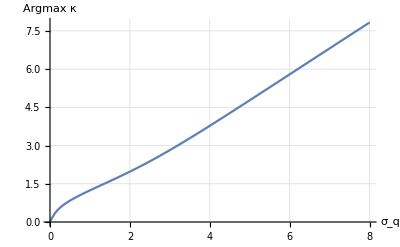

```mathematica
Plot[argmax$ka/.{Subscript[σ, q]->sq},{sq,0.01,8},AxesLabel->{"σ_q","Argmax κ"},GridLines->Automatic]
```

```mathematica
Reduce[dkap==0&&κ>0&&Subscript[σ, q]>0]
```

(0<σ_q<1&&κ==Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2])||(σ_q==1&&κ>0)||(σ_q>1&&κ==Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2])

```mathematica
Plot3D[f$slope$lkstein$mq0[sq^2,ka^2],{ka,0.01,10},{sq,0.01,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Plot[f$slope$lkstein$mq0[sq^2,ka^2],{ka,0.01,20},AxesLabel->Automatic],{sq,0.01,20}]
```

```mathematica
wenkai$lks$mq0$ub[sq1_]:=(sq1-1)^4/(18(sq1-2)^2)
```

```mathematica
wenkai$lks$mq0$ub[Subscript[σ, q]^2]
```

((-1+σ_q^2)^4)/(18 (-2+σ_q^2)^2)

```mathematica
Manipulate[Plot[{f$slope$lkstein$mq0[sq^2,ka^2],wenkai$lks$mq0$ub[sq^2]},{ka,0.01,20},AxesLabel->Automatic],{sq, 0.01,20}]
```

```mathematica
Manipulate[Plot[1/f$slope$lkstein$mq0[sq1,ka1],{ka1,0.01,2}],{sq1,0.01,5}]
```

```mathematica
1/f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]
```

(2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 σ_q^2)^3)/((κ^2)^(5/2) (4+κ^2)^(5/2) (-1+σ_q^2)^4)

```mathematica
reci$f$slope$lkstein$mq0[sq1_,ka1_]:=1/f$slope$lkstein$mq0[sq1,ka1]
```

```mathematica
reci$f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]
```

(2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 σ_q^2)^3)/((κ^2)^(5/2) (4+κ^2)^(5/2) (-1+σ_q^2)^4)

```mathematica
Collect[2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 Subscript[σ, q]^2)^3,Subscript[σ, q]]
```

2 κ^6 (12+20 κ^2+21 κ^4+8 κ^6+κ^8)+12 κ^4 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) σ_q^2+24 κ^2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) σ_q^4+16 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) σ_q^6

```mathematica
D[reci$f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],{κ,1}]//Simplify
```

(8 (κ^2+2 σ_q^2)^2 (κ^2 (12+48 κ^2+95 κ^4+56 κ^6+13 κ^8+κ^10)-(120+180 κ^2+122 κ^4+47 κ^6+10 κ^8+κ^10) σ_q^2))/(κ^5 √(κ^2) (4+κ^2)^(7/2) (-1+σ_q^2)^4)

```mathematica
Solve[D[reci$f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],{κ,1}]==0&&Subscript[σ, q]>0&&κ>0,κ]
```

{{κ→ConditionalExpression[Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2],σ_q>0]}}

```mathematica
slope$lkstein$mq0$ub=f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]/.{κ->Root[#1^12-120 Subscript[σ, q]^2+#1^2 (12-180 Subscript[σ, q]^2)+#1^4 (48-122 Subscript[σ, q]^2)+#1^6 (95-47 Subscript[σ, q]^2)+#1^8 (56-10 Subscript[σ, q]^2)+#1^10 (13-Subscript[σ, q]^2)&,2]}
```

((Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2]^2)^(5/2) (4+Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2]^2)^(5/2) (-1+σ_q^2)^4)/(2 (12+20 Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2]^2+21 Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2]^4+8 Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2]^6+Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2]^8) (Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2]^2+2 σ_q^2)^3)

The following plot shows a tight upper bound of the slope of LKS for any value of σ_q.

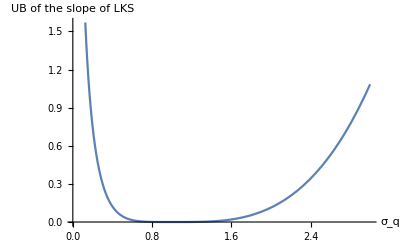

Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2][2]

```mathematica
Plot[N[slope$lkstein$mq0$ub/.{Subscript[σ, q]->sq1}],{sq1,0.01,3},AxesLabel->{Subscript[σ, q],"UB of the slope of LKS"}]
```

```mathematica
D[reci$f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],{κ,2}]//Simplify
```

(8 (κ^8 (300+1280 κ^2+1059 κ^4+360 κ^6+53 κ^8+3 κ^10)+3 κ^4 (192+216 κ^2+660 κ^4+514 κ^6+159 κ^8+18 κ^10+κ^12) σ_q^2-12 κ^2 (-576-748 κ^2-396 κ^4-87 κ^6-κ^8+3 κ^10) σ_q^4+4 (2880+4440 κ^2+2956 κ^4+1098 κ^6+249 κ^8+34 κ^10+3 κ^12) σ_q^6))/(κ^6 √(κ^2) (4+κ^2)^(9/2) (-1+σ_q^2)^4)

```mathematica
Reduce[D[reci$f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2],{κ,2}]>0&&Subscript[σ, q]>0&&κ>0]
```

(0<σ_q<1&&κ>0)||(σ_q>1&&κ>0)

```mathematica
D[f$eff$mq0$le1,κ]//Simplify
```

(2 ⅇ^((-2+σ_q^2)/(2+σ_q^2)) (2+σ_q^2)^(5/2) (κ^2+2 σ_q^2)^2 (κ^2 (12+48 κ^2+95 κ^4+56 κ^6+13 κ^8+κ^10)-(120+180 κ^2+122 κ^4+47 κ^6+10 κ^8+κ^10) σ_q^2))/(κ^5 √(κ^2) (4+κ^2)^(7/2) √(σ_q^2) (-1+σ_q^2)^2 (2+5 σ_q^2+6 σ_q^4+σ_q^6))

```mathematica
Solve[{D[f$eff$mq0$le1,κ]==0,κ>0,Subscript[σ, q]>0},κ]
```

{{κ→ConditionalExpression[Root[#1^12-120 σ_q^2+#1^2 (12-180 σ_q^2)+#1^4 (48-122 σ_q^2)+#1^6 (95-47 σ_q^2)+#1^8 (56-10 σ_q^2)+#1^10 (13-σ_q^2)&,2],0<σ_q<1||σ_q>1]}}

## Assume variance of q is 1

```mathematica
f$slope$lkstein$sq1[mq1_,ka1_]:=f$slope$lkstein[mq1,1,ka1]
```

```mathematica
slope$lkstein$sq1=f$slope$lkstein$sq1[Subscript[μ, q],κ^2]
```

((κ^2)^(5/2) (4+κ^2)^(5/2) μ_q^4)/(2 (2+κ^2) (12+20 κ^2+21 κ^4+8 κ^6+κ^8))